```mathematica
g=9.8(*grav. constant*)
vter = Sqrt[m g/c]

ode1=y''[t]==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]);
ode2 = x''[t]== (-g x'[t]/vter^2) Sqrt[x'[t]^2 + y'[t]^2];
sol = NDSolve[{ode1, ode2, y[0] == x[0] ==0, y'[0] == x'[0] ==3}, {x,y}, {t,0,200}]
```

9.8

3.1305 √(m/c)

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{y''[t]==-9.8 (1+(0.102041 c y'[t] √(x'[t]^2+y'[t]^2))/m),x''[t]==-(1. c x'[t] √(x'[t]^2+y'[t]^2))/m,y[0]==x[0]==0,y'[0]==x'[0]==3},{x,y},{t,0,200}]

```mathematica
myplot1=ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
```

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00408163 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00408163 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 4.08571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

```mathematica
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

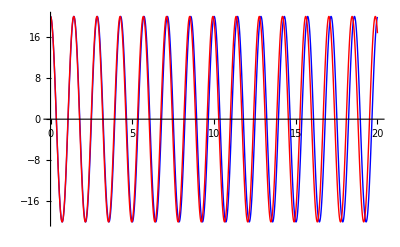

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```